```mathematica
Clear[b,d]
```

```mathematica
sub={b->β,d->δ}
```

{b→β,d→δ}

```mathematica
Solve[(-1+b-v) v==d,v]
```

{{v→1/2 (-1+b-√(1-2 b+b^2-4 d))},{v→1/2 (-1+b+√(1-2 b+b^2-4 d))}}

```mathematica
cp=Solve[{v^2+v-u+d==0,b v-u==0},{v,u}]//Simplify
```

{{v→1/2 (-1+b-√(1-2 b+b^2-4 d)),u→1/2 b (-1+b-√(1-2 b+b^2-4 d))},{v→1/2 (-1+b+√(1-2 b+b^2-4 d)),u→1/2 b (-1+b+√(1-2 b+b^2-4 d))}}

```mathematica
sbd:=1-2 b+b^2-4 d
```

```mathematica
{v,u}/.cp/.{b->β,d->δ}
```

{{1/2 (-1+β-√(1-2 β+β^2-4 δ)),1/2 β (-1+β-√(1-2 β+β^2-4 δ))},{1/2 (-1+β+√(1-2 β+β^2-4 δ)),1/2 β (-1+β+√(1-2 β+β^2-4 δ))}}

```mathematica
%//TeXForm
```

\left(
\begin{array}{cc}
 \frac{1}{2} \left(-\sqrt{\beta ^2-2 \beta -4 \delta +1}+\beta -1\right) & \frac{1}{2}
   \beta  \left(-\sqrt{\beta ^2-2 \beta -4 \delta +1}+\beta -1\right) \\
 \frac{1}{2} \left(\sqrt{\beta ^2-2 \beta -4 \delta +1}+\beta -1\right) & \frac{1}{2} \beta
    \left(\sqrt{\beta ^2-2 \beta -4 \delta +1}+\beta -1\right) \\
\end{array}
\right)

```mathematica
cp={{v->1/2 (-1+b-s),u->1/2 b (-1+b-s)},{v->1/2 (-1+b+s),u->1/2 b (-1+b+s)}}
```

{{v→1/2 (-1+b-s),u→1/2 b (-1+b-s)},{v→1/2 (-1+b+s),u→1/2 b (-1+b+s)}}

```mathematica
grad=Grad[{v^2+v-u+d,b v-u},{v,u}]
```

{{1+2 v,-1},{b,-1}}

```mathematica
{lam1,lam2}=Eigenvalues[grad]
```

{v-√(1-b+2 v+v^2),v+√(1-b+2 v+v^2)}

```mathematica
lam1/.cp//FullSimplify
```

{1/2 (-1+b-s)-√(-s+1/4 (1-b+s)^2),1/2 (-1+b+s)-√(s+1/4 (-1+b+s)^2)}

```mathematica
(v+1)^2-b/.cp
```

{-b+(1+1/2 (-1+b-s))^2,-b+(1+1/2 (-1+b+s))^2}

```mathematica
Reduce[{1-2 b+b^2-4 d>=0&&1/4 (1-b+√(1-2 b+b^2-4 d))^2-√(1-2 b+b^2-4 d)>=0},{b,d}]
```

(b≤0&&d≤1/4 (1-2 b+b^2))||(0<b<1&&(d≤-2 b-√(b+2 b^2+b^3)||-2 b+√(b+2 b^2+b^3)≤d≤1/4 (1-2 b+b^2)))||(b==1&&(d≤-4||d==0))||(b>1&&(d≤-2 b-√(b+2 b^2+b^3)||-2 b+√(b+2 b^2+b^3)≤d≤1/4 (1-2 b+b^2)))

```mathematica
lam2/.cp//Simplify
```

{1/2 (-1+b-√(1-2 b+b^2-4 d))+√(1/4 (1-b+√(1-2 b+b^2-4 d))^2-√(1-2 b+b^2-4 d)),1/2 (-1+b+√(1-2 b+b^2-4 d))+√(1/4 (-1+b+√(1-2 b+b^2-4 d))^2+√(1-2 b+b^2-4 d))}

```mathematica
Reduce
```

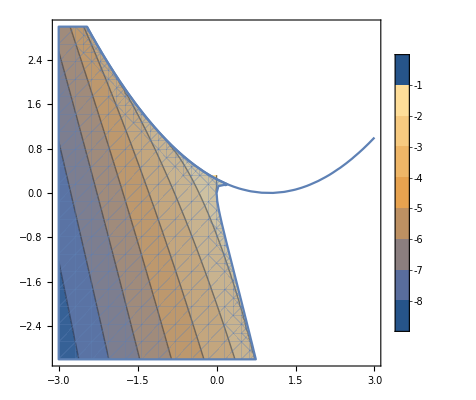

```mathematica
Show[

ContourPlot[1/2 (-1+b-√(1-2 b+b^2-4 d))-√(1/4 (1-b+√(1-2 b+b^2-4 d))^2-√(1-2 b+b^2-4 d)),{b,-3,3},{d,-3,3},PlotLegends->Automatic],RegionPlot[(b≤0&&d≤1/4 (1-2 b+b^2))||(0<b<1&&(d≤-2 b-√(b+2 b^2+b^3)||-2 b+√(b+2 b^2+b^3)≤d≤1/4 (1-2 b+b^2)))||(b==1&&(d≤-4||d==0))||(b>1&&(d≤-2 b-√(b+2 b^2+b^3)||-2 b+√(b+2 b^2+b^3)≤d≤1/4 (1-2 b+b^2))),{b,-3,3},{d,-3,3}],
ContourPlot[1-2 b+b^2-4 d==0,{b,-3,3},{d,-3,3}]
]
```

```mathematica
tp=((v+1)^2-b/.v->(b(b-1))/2//FullSimplify)
```

1/4 (-1+b)^2 (4+b^2)

```mathematica
{l1,l2}={v-t,v+t}/.{v->(b(b-1))/2,t->√tp}//FullSimplify
```

{1/2 ((-1+b) b-√((-1+b)^2 (4+b^2))),1/2 ((-1+b) b+√((-1+b)^2 (4+b^2)))}

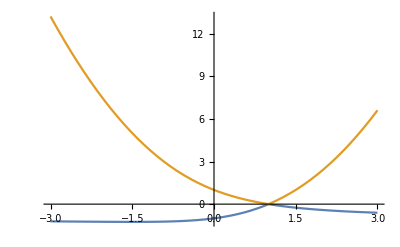

```mathematica
Plot[{l1,l2},{b,-3,3}]
```

```mathematica
D[{l1,l2},b]//FullSimplify
```

{-1/2+b+((-1+b) (-4+b-2 b^2))/(2 √((-1+b)^2 (4+b^2))),-1/2+b+((-1+b) (4+b (-1+2 b)))/(2 √((-1+b)^2 (4+b^2)))}

```mathematica
%//TeXForm
```

\left\{\frac{(b-1) \left(-2 b^2+b-4\right)}{2 \sqrt{(b-1)^2
   \left(b^2+4\right)}}+b-\frac{1}{2},\frac{(b-1) (b (2 b-1)+4)}{2 \sqrt{(b-1)^2
   \left(b^2+4\right)}}+b-\frac{1}{2}\right\}

```mathematica
F[v_,u_,d_,b_]:={v^2+v-u+d,b v-u}
```

```mathematica
Manipulate[
With[{d=(1-b)^2/4},
StreamPlot[F[v,u,d,b],{v,-2,5},{u,-2,5},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{v,u}]/.NSolve[#==0&/@F[v,u,d,b],{v,u}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@b]
]],{b,-3,3,0.1}
]
```

NSolve::nsmet: この系はNSolveで利用できるメソッドでは解けません

ReplaceAll::reps: {NSolve[F[v==0,u==0,False,False],{v,u}]}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Join::heads: 位置1と2での頭部ListとReplaceAllは等しいことが想定されています．

NSolve::nsmet: この系はNSolveで利用できるメソッドでは解けません

ReplaceAll::reps: {NSolve[F[v==0,u==0,False,False],{v,u}]}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Join::heads: 位置1と2での頭部ListとReplaceAllは等しいことが想定されています．

NSolve::nsmet: この系はNSolveで利用できるメソッドでは解けません

General::stop: この計算中に，NSolve::nsmetのこれ以上の出力は表示されません．

ReplaceAll::reps: {NSolve[F[v==0,u==0,False,False],{v,u}]}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Join::heads: 位置1と2での頭部ListとReplaceAllは等しいことが想定されています．

General::stop: この計算中に，Join::headsのこれ以上の出力は表示されません．

```mathematica
(* *)
```

```mathematica
tp=1-b+2 v+v^2/.cp//Simplify
```

{-s+1/4 (1-b+s)^2,s+1/4 (-1+b+s)^2}

```mathematica
tp/.s->√sbd//FullSimplify
```

{1/4 (1-b+√((-1+b)^2-4 d))^2-√((-1+b)^2-4 d),1/4 (-1+b+√((-1+b)^2-4 d))^2+√((-1+b)^2-4 d)}

```mathematica
v-√tp[[2]]/.cp[[2]]/.s->√sbd/.sub//FullSimplify//TeXForm
```

\frac{1}{2} \left(\sqrt{(\beta -1)^2-4 \delta }+\beta -1\right)-\sqrt{\frac{1}{4} \left(\sqrt{(\beta -1)^2-4 \delta }+\beta -1\right)^2+\sqrt{(\beta -1)^2-4 \delta }}

```mathematica
%//TeXForm
```

\frac{1}{2} \left(\sqrt{b^2-2 b-4 d+1}+b-1\right)-\sqrt{\frac{1}{4} \left(\sqrt{b^2-2 b-4 d+1}+b-1\right)^2+\sqrt{b^2-2 b-4 d+1}}

```mathematica
Reduce[Evaluate[v-√tp[[2]]/.cp[[2]]/.s->√sbd]==0,{b,d}]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==1/2 (-1+b-√(1+Times[«2»]+Power[«2»]))}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

0==1/2 (-1+b-√(1-2 b+b^2))&&d==1/4 (-1+b)^2

```mathematica
v-√tp/.cp[[2]]
```

{1/2 (-1+b+s)-√(-s+1/4 (1-b+s)^2),1/2 (-1+b+s)-√(s+1/4 (-1+b+s)^2)}

```mathematica
Reduce[1/4 (1-b+√(1-2 b+b^2-4 d))^2-√(1-2 b+b^2-4 d)<0,{b,d}]
```

b>0&&-2 b-√(b+2 b^2+b^3)<d<-2 b+√(b+2 b^2+b^3)

```mathematica
%/.{b->β,d->δ}//TeXForm
```

\beta >0\land -\sqrt{\beta ^3+2 \beta ^2+\beta }-2 \beta <\delta <\sqrt{\beta ^3+2 \beta ^2+\beta }-2 \beta

```mathematica
cp/.s->√sbd
```

{{v→1/2 (-1+b-√(1-2 b+b^2-4 d)),u→1/2 b (-1+b-√(1-2 b+b^2-4 d))},{v→1/2 (-1+b+√(1-2 b+b^2-4 d)),u→1/2 b (-1+b+√(1-2 b+b^2-4 d))}}

```mathematica
Reduce[1/2 (-1+b-√(1-2 b+b^2-4 d))>0,{b,d}]
```

b>1&&0<d≤1/4 (1-2 b+b^2)

```mathematica
Reduce[1/2 (-1+b+√(1-2 b+b^2-4 d))>0,{b,d}]
```

(b≤1&&d<0)||(b>1&&d≤1/4 (1-2 b+b^2))

```mathematica
Reduce[1/4 (-1+b+√(1-2 b+b^2-4 d))^2+√(1-2 b+b^2-4 d)0,{b,d}]
```

Reduce::naqs: 1/4 (-1+b+√(1-2 b+b^2-4 d))^2 is not a quantified system of equations and inequalities.

Reduce[1/4 (-1+b+√(1-2 b+b^2-4 d))^2,{b,d}]

```mathematica
Rtn1=b>0&&-2 b-√(b+2 b^2+b^3)<d<-2 b+√(b+2 b^2+b^3)&&1-2 b+b^2-4 d>0
```

b>0&&-2 b-√(b+2 b^2+b^3)<d<-2 b+√(b+2 b^2+b^3)&&1-2 b+b^2-4 d>0

```mathematica
Rtn2=(b<1&&d≤1/4 (1-2 b+b^2))||(b==1&&d<0)||(b>1&&d≤1/4 (1-2 b+b^2))
```

(b<1&&d≤1/4 (1-2 b+b^2))||(b==1&&d<0)||(b>1&&d≤1/4 (1-2 b+b^2))

```mathematica
Rvp1=1/2 (-1+b-√(1-2 b+b^2-4 d))>=0&&1-2 b+b^2-4 d>0
```

1/2 (-1+b-√(1-2 b+b^2-4 d))≥0&&1-2 b+b^2-4 d>0

```mathematica
Rvp2=(b≤1&&d<0)||(b>1&&d≤1/4 (1-2 b+b^2))
```

(b≤1&&d<0)||(b>1&&d≤1/4 (1-2 b+b^2))

```mathematica
Reduce[1/2 (-1+b-√(1-2 b+b^2-4 d))>0,d]
```

b>1&&0<d≤1/4 (1-2 b+b^2)

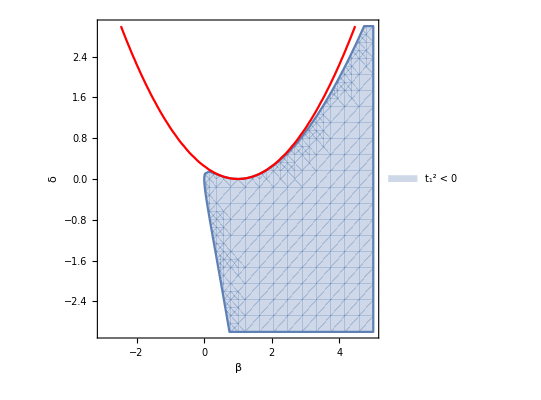

```mathematica
Show[
RegionPlot[{Rtn},{b,-3,5},{d,-3,3},Axes->True,AxesLabel->{"β","δ"},PlotLegends->{"t_1^2 < 0"}],
ContourPlot[1-2 b+b^2-4 d==0,{b,-3,5},{d,-3,3},ContourStyle->Red]
]
```

```mathematica
D
```

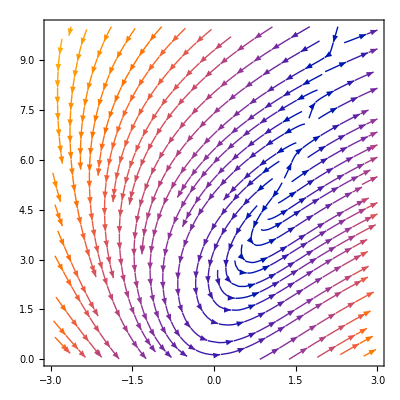

```mathematica
StreamPlot[{v^2+v-u+2.5,4.25v-u},{v,-3,3},{u,0,10}]
```

```mathematica
P[x_,y_,z_]:=z^2 Tan[x y^3]Sec[x y^3] y^3
```

```mathematica
Q[x_,y_,z_]:=z^2 Tan[x y^3]Sec[x y^3] 3x y^2+2x^2
```

```mathematica
R[x_,y_,z_]:=2z Sec[x y^3]+x^2
```

```mathematica
D[R[x,y,z],y]-D[Q[x,y,z],z]//Simplify
```

0

```mathematica
D[P[x,y,z],z]-D[R[x,y,z],x]//Simplify
```

-2 x

```mathematica
D[Q[x,y,z],x]-D[P[x,y,z],y]//Simplify
```

4 x

```mathematica
x=(2Cos@t)/(√5)
```

(2 Cos[t])/(√5)

```mathematica
√(1-(1/2)^2)
```

(√3)/2

```mathematica
Reduce[{x^2+y^2+z^2==1,2y+z==1},{y,z}]
```

(y==2/5 (1-√(1-Cos[t]^2))||y==2/5 (1+√(1-Cos[t]^2)))&&z==1-2 y

```mathematica
y=2/5(1-Sin@t);z=1-2y
```

1-4/5 (1-Sin[t])

```mathematica
{x,y,z}//Simplify
```

```mathematica
Solve[1/5 (1+4 Sin[t])==0,t]//Normal
```

{{t→-ArcSin[1/4]+2 π C[1]},{t→π+ArcSin[1/4]+2 π C[1]}}

```mathematica
NIntegrate[FullSimplify[z^2 Tan[x y^3]Sec[x y^3]{y^3,3x y^2,0}+2z Sec[x y^3]{0,0,1}+x^2 {0,2,1}].D[{x,y,z},t],{t,Pi+ArcSin[1/4],-ArcSin[1/4]}]
```

NIntegrate::slwcon: 数値積分の収束が遅すぎます．特異性がある，積分の値がゼロ，被積分関数が激しく振動する，あるいはWorkingPrecisionが小さすぎるのいずれかが原因である可能性があります．

NIntegrate::ncvb: NIntegrateが{t} = {0.488164}の近傍のtで二分法を9回反復しましたが，指定された確度に収束しませんでした．NIntegrateは積分と誤差推定として9.19403×10^-17と2.03537×10^-16を得ました．

9.19403×10^-17

```mathematica
Integrate[z^2 Tan[x y^3]Sec[x y^3]{y^3,3x y^2,0}+2z Sec[x y^3]{0,0,1}+x^2 {0,2,1}]
```

```mathematica
(2Cos@t)/(√5)/.{{t->-ArcSin[1/4]},{t->π+ArcSin[1/4]}}
```

{(√3)/2,-(√3)/2}

```mathematica
Solve[m x-3x^2==x,x]
```

{{x→0},{x→1/3 (-1+m)}}

```mathematica
g[x_,m_]:=m x-3x^2
```

```mathematica
D[g[x,m],x]/.{x->1/3(m-1)}//Simplify
```

2-m

```mathematica
With[{d=0.1},Show[
StreamPlot[F[v,u,d],{v,-6,6},{u,-6,6},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{v,u}]/.NSolve[#==0&/@F[v,u,d,b],{v,u}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@b]<>" Critical points: "<>ToString[NumberForm[{v,u}/.NSolve[#==0&/@F[v,u,d],{v,u}],2]],ImageSize->Medium,StreamColorFunction->None,StreamPoints->{{{{1.9,5.6},Red},Automatic}},ImageSize->Full
]
]]
```

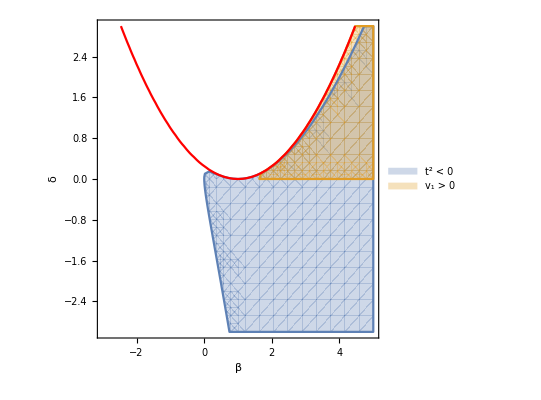

```mathematica
Show[
RegionPlot[{Rtn,Rvp1},{b,-3,5},{d,-3,3},Axes->True,AxesLabel->{"β","δ"},PlotLegends->{"t^2 < 0", "v_1 > 0", "v_2 > 0"}],
ContourPlot[1-2 b+b^2-4 d==0,{b,-3,5},{d,-3,3},ContourStyle->Red]
]
```

```mathematica
Minimize[(√b)/2+1/4 (-3 b+b^2),b]//FullSimplify
```

{0,{b→0}}

```mathematica
F[v,u,d,b]
```

{d-u+v+v^2,-u+b v}

```mathematica
i=1
```

1

```mathematica
plt1=Show[RegionPlot[{Rtn,Rvp},{b,-5,5},{d,-5,5},Axes->True,AxesLabel->{"β","δ"},PlotLegends->{"t^2 < 0", "v_1 > 0", "v_2 > 0"}],
ContourPlot[1-2 b+b^2-4 d==0,{b,-5,5},{d,-5,5},ContourStyle->Red]];
Manipulate[{
Show[
plt1,
Graphics[Locator[{b,d}],PlotRange->2,ImagePadding->20,Frame->True,ImageSize->Medium,Axes->True],ImageSize->Medium
],
img=StreamPlot[F[v,u,d,b],{v,-s,s},{u,-s,s},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{v,u}]/.NSolve[#==0&/@F[v,u,d,b],{v,u}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@b],ImageSize->Medium
],Button["Save",Export[NotebookDirectory[]<>"\\images\\img,b="<>ToString[b]<>",d="<>ToString[d]<>".png",img]]
},{{d,0},-5,5},{{b,2},-5,5},{{s,5},0.1,40,0.1}]
```

```mathematica
(*P1*)
```

```mathematica
v-√tp[[1]]/.cp[[1]]//FullSimplify
```

1/2 (-1+b-s)-√(-s+1/4 (1-b+s)^2)

```mathematica
Reduce[1/2 (-1+b-s)-√(-s+1/4 (1-b+s)^2)<0&&s>0,{s,b}]
```

s>0&&b≤1-2 √s+s

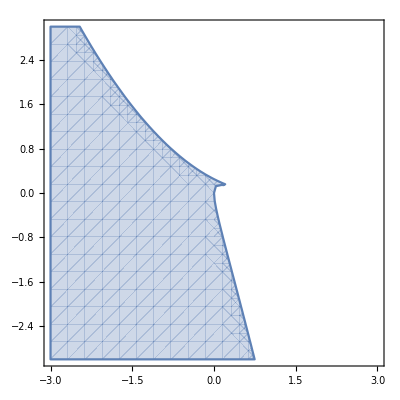

```mathematica
RegionPlot[Evaluate@Reduce[1/2 (-1+b-√((-1+b)^2-4 d))-√(1/4 (1-b+√((-1+b)^2-4 d))^2-√((-1+b)^2-4 d))<0,{b,d}],{b,-3,3},{d,-3,3}]
```

```mathematica
Eigenvalues[Grad[F[v,u,0.08,0.024],{v,u}]/.sol[[1]]]
```

{-0.933445,-0.639397}

```mathematica
Minimize[1/2 (-1+b-s)-√(1/4 (-1+b-s)^2-s),{b,s}]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{b→Indeterminate,s→Indeterminate}}

```mathematica
v-√tp
```

{-s+1/4 (1-b+s)^2,s+1/4 (-1+b+s)^2}

```mathematica
-3+2 b+b^2-8 v/.v->1/2 (-b+b^2-b s)//Simplify
```

-3-3 b^2+b (6+4 s)

```mathematica
Factor[-3-3 b^2+b (6+4 s)]
```

-3+6 b-3 b^2+4 b s

```mathematica
s=√((1-b)^2-4d)
```

√((1-b)^2-4 d)

```mathematica
4b s-3(1-b)^2//Simplify//Expand
```

```mathematica
-4 b √(1-2 b+b^2-4 d)/.{b->2,d->0.21484375}
```

-6.

```mathematica
Solve[(-3+6 b-3 b^2)^2==(4 b √(1-2 b+b^2-4 d))^2,d]
```

{{d→(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)}}

```mathematica
Reduce[-3+6 b-3 b^2+4 b √(1-2 b+b^2-4 d)==0,d]
```

Reduce::useq: Reduceで求められた解に未解決の方程式{0==-(3 (-1+2 b+√(Power[«2»] Power[«2»]) b-b^2))/(4 b)}が含まれています．これは一式の解がWolfram言語関数の分枝切断線に依存しているためであると考えられます．

b≠0&&0==-(3 (-1+2 b+√((-1+b)^4/b^2) b-b^2))/(4 b)&&d==((-1+b)^2 (-9+18 b+7 b^2))/(64 b^2)

```mathematica
With[{b=2},(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)//N]
```

0.214844

```mathematica
Solve[-3+6 b-3 b^2-4 b √(1-2 b+b^2-4 d)==0,d]
```

Solve::nongen: 解はパラメータのすべての値に対しては有効ではない可能性があります．

{{d→(-9+36 b-38 b^2+4 b^3+7 b^4)/(64 b^2)}}

```mathematica
-3+6 b-3 b^2+4 b √(1-2 b+b^2-4 d)
```

```mathematica
Point[{u,v}]/.NSolve[#==0&/@F[u,v],{u,v}]
```

{Point[{1.7746,0.887298}],Point[{0.225403,0.112702}]}

```mathematica
Evaluated[Point[{u,v}]/.NSolve[#==0&/@F[u,v],{u,v}]]
```

Evaluated[{Point[{1.7746,0.887298}],Point[{0.225403,0.112702}]}]

```mathematica
F[u_,v_,d_,b_]:={v^2+v-u+d,b v-u}
```

```mathematica
NSolve[#==0&/@F[u,v],{u,v}]
```

{{u→1.7746,v→0.887298},{u→0.225403,v→0.112702}}

```mathematica
Clear[s]
```

```mathematica
T=√((1-b)^2-4 √((1-b)^2-4d))
```

√((1-b)^2-4 √((1-b)^2-4 d))

```mathematica
Reduce[(1-b)^2-4 √((1-b)^2-4d)<0,{b,d}]
```

b∈ℝ&&d<1/64 (15-28 b+10 b^2+4 b^3-b^4)

```mathematica
1/64 (15-28 b+10 b^2+4 b^3-b^4)/.{b->2}
```

15/64

```mathematica
-1+b+T//Simplify
```

-1+b+√(1-2 b+b^2-4 √(1-2 b+b^2-4 d))

```mathematica
Reduce[-1+b-T0,{b,d}]
```

b<1&&1/64 (15-28 b+10 b^2+4 b^3-b^4)≤d≤1/4 (1-2 b+b^2)

```mathematica
Reduce[-1+b+T<0,{b,d}]
```

b<1&&1/64 (15-28 b+10 b^2+4 b^3-b^4)≤d<1/4 (1-2 b+b^2)

```mathematica
-1+b-√(1-2 b+b^2+4 √(1-2 b+b^2-4 d))/.{b->2,d->0.1}
```

-1.02445

```mathematica
Maximize[-1+b+√(1-2 b+b^2-4 √(1-2 b+b^2-4 d)),{b,d}]
```

Maximize::natt: 指定の制約条件を満足するどの点においても，最大値に達していません．

{∞,{b→Indeterminate,d→Indeterminate}}

```mathematica
Maximize[-1+b-√(1-2 b+b^2-4 √(1-2 b+b^2-4 d)),{b,d}]
```

{0,{b→2,d→1/4}}

```mathematica
Reduce[-1+b+√(1-2 b+b^2+4 √(1-2 b+b^2-4 d))<=0,{b,d}]
```

(b==1&&d==0)||(b<1&&d==1/4 (1-2 b+b^2))

```mathematica
Reduce[-1+b+T<=00,d]
```

(b==1&&d==0)||(b<1&&d==1/4 (1-2 b+b^2))

```mathematica
Reduce[-1+b-T==0,d]
```

Reduce::useq: Reduceで求められた解に未解決の方程式{0==-1+b-√(1-2 b+b^2)}が含まれています．これは一式の解がWolfram言語関数の分枝切断線に依存しているためであると考えられます．

0==-1+b-√(1-2 b+b^2)&&d==1/4 (-1+b)^2

```mathematica
Reduce[-1+b-√□]
```

```mathematica
-3+2 bb+bb^2-8 v/.v->1/2 (-1+bb-s)//Simplify
```

1-2 bb+bb^2+4 s

```mathematica
-3+2 bb+bb^2-8 v/.v->1/2 (-1+bb+s)//Simplify
```

1-2 bb+bb^2-4 s

```mathematica
With[{d=0.24,b=0},
Print@Eigenvalues@({{-1, 1+2 v}, {-1, bb}});
Print@Eigenvalues@({{-1, 1+2 v}, {-1, b}});
Print@Eigenvalues@({{-1, 1+(b-1)}, {-1, b}});
s=√((1-b)^2-4d);
Print@s;
t=√(4s-(1-b)^2);
Print@t;
Print@{{b/2(b-1-√((1-b)^2-4d)),1/2(b-1-√((1-b)^2-4d))},
{b/2(b-1+√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))}};
Print@{1/2(-1+b-t),1/2(-1+b+t)}
]
```

{1/2 (-1+bb-√(-3+2 bb+bb^2-8 v)),1/2 (-1+bb+√(-3+2 bb+bb^2-8 v))}

{1/2 (-1-√(-3-8 v)),1/2 (-1+√(-3-8 v))}

{-1,0}

0.

0.+1.73205 ⅈ

{{0.,-0.5},{0.,-0.5}}

{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

```mathematica
Eigenvalues@({{-1, 1+2 v}, {-1, b}})
```

{1/2 (-1+b-√(-3+2 b+b^2-8 v)),1/2 (-1+b+√(-3+2 b+b^2-8 v))}

```mathematica
{1/2 (-1+b-√(-3+2 b+b^2-8 v)),1/2 (-1+b+√(-3+2 b+b^2-8 v))}/.{b->3,v->1}
```

{0,2}

```mathematica
1/64 (15-28 b+10 b^2+4 b^3-b^4)/.{b->1}
```

0

```mathematica
0.81/4
```

0.2025

```mathematica
F[u,v,d,b]
```

{d-u+v+v^2,-u+b v}

```mathematica
D[F[u,v,d,b][[1]],u]+D[F[u,v,d,b][[2]],v]
```

-1+b

```mathematica
Eigenvectors[{{-1,5},{-1,3}}]
```

{{2-ⅈ,1},{2+ⅈ,1}}

```mathematica
Eigenvalues[{{-1,5},{-1,3}}]
```

{1+ⅈ,1-ⅈ}

```mathematica
{{3,1},{-1,1}}
```

```mathematica
F[u,v,0,2]
```

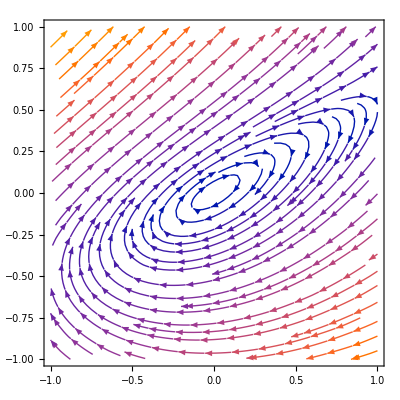

```mathematica
StreamPlot[{-u+2 v,-u+v+v^2},{u,-1,1},{v,-1,1}]
```

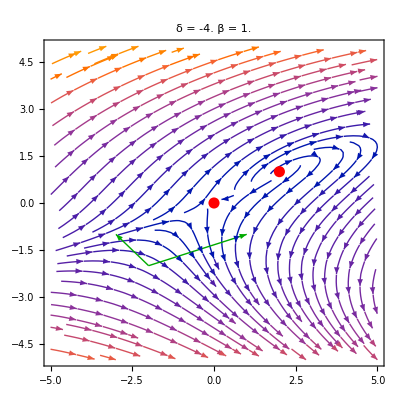

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\Q3a1.png

```mathematica
img=Show[
StreamPlot[F[u,v,0,2],{u,-5,5},{v,-5,5},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,0,2],{u,v}]),
PlotLabel->"δ = "<>ToString[N@-4]<>"  β = "<>ToString[N@1]
],
Graphics[{Darker@Green,Arrow[{{{-2,-2},{-2,-2}+{3,1}},{{-2,-2},{-2,-2}+{-1,1}}}]}]
]
Export[NotebookDirectory[]<>"images\\Q3a1.png",img]
```

```mathematica
ReplaceAll[Grad[F[u,v,-1,1],{u,v}],Solve[Evaluate[#==0&/@F[u,v,-1,1]],{u,v}]]
```

{{{-1,-1},{-1,1}},{{-1,3},{-1,1}}}

```mathematica
Print[Evaluate[ReplaceAll[Grad[F[u,v,d,1],{u,v}],Solve[#==0&/@F[u,v,d,1],{u,v}]]/.{d->-3}]]
```

{{{-1,1+2 √3},{-1,1}},{{-1,1-2 √3},{-1,1}}}

```mathematica
Eigenvectors[ReplaceAll[Grad[F[u,v,-d,1],{u,v}],Solve[#==0&/@F[u,v,-d,1],{u,v}]][[1]]]
```

{{1+√2 d^(1/4),1},{1-√2 d^(1/4),1}}

```mathematica
Manipulate[
With[{d=dd},
Re@Eigenvectors[ReplaceAll[Grad[F[u,v,-d,1],{u,v}],Solve[#==0&/@F[u,v,-d,1],{u,v}]][[1]]]],{dd,-5,3,0.1}]
```

Solve::naqs: F[u==0,v==0,False,False] is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Solve[F[u==0,v==0,False,False],{u,v}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
dat=Table[
With[{},
StreamPlot[F[u,v,d,2],{u,-20,50},{v,-50,20},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,d,2],{u,v}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@3],StreamPoints->200
]
],{d,-5,3,0.1}];
Export[NotebookDirectory[]<>"images\\Q3a2.gif",dat]
```

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\Q3a2.gif

```mathematica
|
```

```mathematica
dat=Table[
StreamPlot[F[u,v,d,1],{u,-10,10},{v,-10,10},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,d,1],{u,v}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@1]
],{d,-5,3,0.1}
];
Export[NotebookDirectory[]<>"images\\center.gif",dat]
```

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\center.gif

```mathematica
V[u_,v_]:=u^2+(v-1/2)^2
```

```mathematica
Dot[Grad[V[u,v],{u,v}],F[u,v,d,1]]//FullSimplify
```

v (-1+2 v)+u (1+2 d-2 u+2 v^2)

```mathematica
Manipulate[
StreamPlot[F[u,v,d,b],{u,-10,10},{v,-10,10},
Epilog->{Red,PointSize[0.02]}~Join~(Point[{u,v}]/.NSolve[#==0&/@F[u,v,d,b],{u,v}]),
PlotLabel->"δ = "<>ToString[N@d]<>"  β = "<>ToString[N@b],ImageSize->Large
],{d,-5,5,0.01},{b,-5,5,0.01}
]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[F[u==0,v==0,False,False],{u,v}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[F[u==0,v==0,False,False],{u,v}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

General::stop: Further output of NSolve::nsmet will be suppressed during this calculation.

ReplaceAll::reps: {NSolve[F[u==0,v==0,False,False],{u,v}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
NSolve[{v^2+v-u+0.1==0,2v-u==0},{u,v}]
```

{{u→1.7746,v→0.887298},{u→0.225403,v→0.112702}}

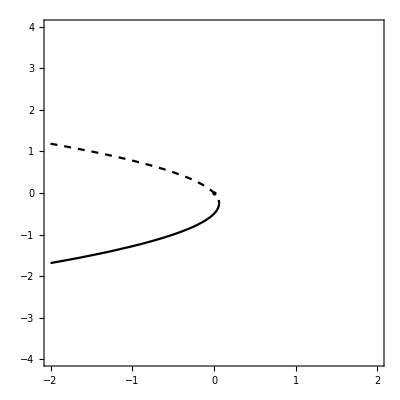

```mathematica
f1[v_,r_]:=v^2+v-v/2+r
λ=D[f1[x,r],x];
Show[ContourPlot[{ConditionalExpression[f1[x,r],λ<0]==0,ConditionalExpression[f1[x,r],λ>0]==0},{r,-2,2},{x,-4,4},ContourStyle->{{Black},{Black,Dashed}},
Epilog->{Point[{0,0}]}
]]
```

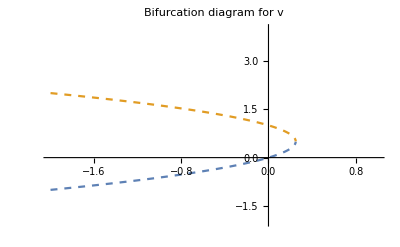

```mathematica
Plot[
{1/2(1-√(1-4d)),1/2(1+√(1-4d))},{d,-2,1},PlotStyle->Dashed,PlotLabel->"Bifurcation diagram for v",PlotRange->{{-2,1},{-2,4}}
]
```

```mathematica
Clear[b,d]
```

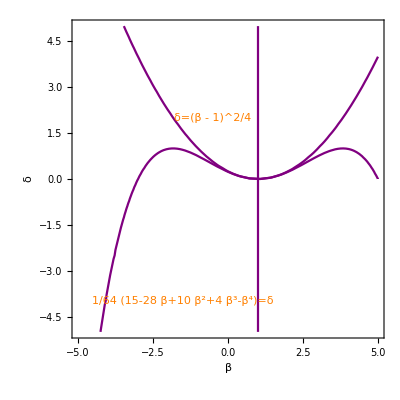

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\region.png

```mathematica
img=Show[
(*ContourPlot[b/2(b-1-√((1-b)^2-4d)),{b,-5,5},{d,-5,5},Contours->100,ContourStyle->None,BaseStyle->Directive[Opacity[0.7]]],*)
ContourPlot[{1/64 (15-28 b+10 b^2+4 b^3-b^4)==d,d==(b-1)^2/4,b==1},{b,-5,5},{d,-5,5},ContourStyle->Purple,FrameLabel->{"β","δ"}],
Graphics[{Orange,Text["1/64 (15-28 β+10 β^2+4 β^3-β^4)=δ",{-1.5,-4}],Text["δ=(β - 1)^2/4",{-0.5,2}]}]
]
Export[NotebookDirectory[]<>"images\\region.png",img]
```

```mathematica
ani=Animate[
Show[Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{b,-10,1},PlotRange->{{-10,10},{-10,20}},PlotLabel->"u, b = "<>ToString[b]],
Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{b,1,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->Dashed,PlotLabel->"u, b = "<>ToString[b]]
]
,{d,-5,5}
]
```

```mathematica
dat=Table[
Show[Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{b,-10,1},PlotRange->{{-10,10},{-10,20}},PlotLabel->"u, δ = "<>ToString[d]],
Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{b,1,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->Dashed,PlotLabel->"u, δ = "<>ToString[d]]
]
,{d,-5,5,0.05}];
Export[NotebookDirectory[]<>"images\\ani_du.gif",dat]
```

Experimental`OptimizeExpression::dupsym: The symbol $6040 with context Compile` already exists.

Experimental`OptimizeExpression::dupsym: The symbol $6080 with context Compile` already exists.

Experimental`OptimizeExpression::dupsym: The symbol $7015 with context Compile` already exists.

General::stop: Further output of Experimental`OptimizeExpression::dupsym will be suppressed during this calculation.

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\ani_du.gif

```mathematica
dat=Table[
Show[Plot[{1/2(b-1-√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))},{b,-10,1},PlotRange->{{-10,10},{-10,20}},PlotLabel->"u, δ = "<>ToString[d]],
Plot[{1/2(b-1-√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))},{b,1,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->Dashed,PlotLabel->"v, δ = "<>ToString[d]]
]
,{d,-5,5,0.05}];
Export[NotebookDirectory[]<>"images\\ani_dv.gif",dat]
```

Experimental`OptimizeExpression::dupsym: The symbol $11043 with context Compile` already exists.

Experimental`OptimizeExpression::dupsym: The symbol $11103 with context Compile` already exists.

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\ani_dv.gif

```mathematica
Save["ani.gif",ani]
```

```mathematica
dat=Table[Show[Plot[{b/2(b-1-√((1-b)^2-4d)),b/2(b-1+√((1-b)^2-4d))},{d,-10,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->If[b<=1,{Dashed,Automatic},Dashed],PlotLabel->"u, b = "<>ToString[b]],
ParametricPlot[{(1-x)^2/4,(x(x-1))/2},{x,-10,10},PlotStyle->{Gray,Dotted}
]
],{b,-3,3,0.02}];
Export[NotebookDirectory[]<>"images\\ani_u.gif",dat]
```

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\ani_u.gif

```mathematica
dat=Table[Show[Plot[{1/2(b-1-√((1-b)^2-4d)),1/2(b-1+√((1-b)^2-4d))},{d,-10,10},PlotRange->{{-10,10},{-10,20}},PlotStyle->If[b<=1,{Dashed,Automatic},Dashed],PlotLabel->"v, b = "<>ToString[b]],
ParametricPlot[{(1-x)^2/4,(x-1)/2},{x,-10,10},PlotStyle->{Gray,Dotted}
]
],{b,-3,3,0.02}];
Export[NotebookDirectory[]<>"images\\ani_v.gif",dat]
```

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\images\ani_v.gif

```mathematica
NotebookDirectory[]
```

E:\assignments\2023-05-14-ODE-Math-7131-Ass3\

```mathematica
Export["uv.png",ParametricPlot[{(b(b-1))/2,(b-1)/2},{b,-5,5},PlotLabel->"uv bifurcation point"]]
```

uv.png

```mathematica
Plot[]
```